```mathematica
a1[a_,r_,s_,ϵ_,θ_,l_]:=(1+l) (r^(1+2 l)-s^(1+2 l))(-1+ϵ) (1+l+l ϵ);
a2[a_,r_,s_,ϵ_,θ_,l_]:=(1+l) (1+2 l) r^(1+2 l)  (-1+ϵ);
b1[a_,r_,s_,ϵ_,θ_,l_]:= -r^(1+2 l) (l (1+l) r^(1+2 l) (-1+ϵ)^2-s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
b2[a_,r_,s_,ϵ_,θ_,l_]:=(1+2 l) r^(1+2 l) s^(1+2 l) (1+l+l ϵ);
b3[a_,r_,s_,ϵ_,θ_,l_]:=(1+2 l)^2 r^(1+2 l) s^(1+2 l) ϵ;
c1[a_,r_,s_,ϵ_,θ_,l_]:=-(1+l) (r^(1+2 l)-s^(1+2 l))(1+l+l ϵ) θ;
c2[a_,r_,s_,ϵ_,θ_,l_]:=-(1+l) (1+2 l) r^(1+2 l) ϵ θ;
d1[a_,r_,s_,ϵ_,θ_,l_]:=-a^(1+2 l) l (r^(1+2 l)-s^(1+2 l)) (1+l+l ϵ) θ;
d2[a_,r_,s_,ϵ_,θ_,l_]:=-l((1+l) r^(2+4 l) (-1+ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ)+a^(1+2 l) (r^(1+2 l)-s^(1+2 l)) (1+l+l ϵ)) θ;
d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
```

C:\Users\DANIEL\Desktop\Physics\TESIS\Avances

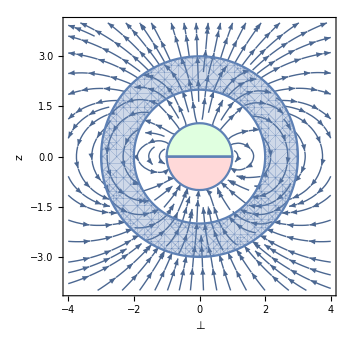

electric_general.png

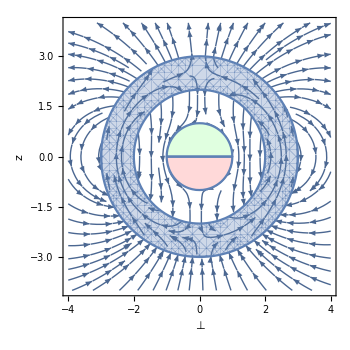

magnetic_general.png

```mathematica
(*GENERAL CASE*)

SetDirectory[NotebookDirectory[]]
ϕ[r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,2,3,4,1,l]*
(Boole[1≤r≤2](a1[1,2,3,4,1,l]*r^l+b1[1,2,3,4,1,l]*r^(-l-1))+
Boole[2≤r≤3](a2[1,2,3,4,1,l]*r^l+b2[1,2,3,4,1,l]*r^(-l-1))+
Boole[3≤r](b3[1,2,3,4,1,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,2,3,4,1,2l]*
(Boole[1≤r≤2](a1[1,2,3,4,1,2l]*r^(2l)+b1[1,2,3,4,1,2l]*r^(-2l-1))+
Boole[2≤r≤3](a2[1,2,3,4,1,2l]*r^(2l)+b2[1,2,3,4,1,2l]*r^(-2l-1))+
Boole[3≤r](b3[1,2,3,4,1,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas y derivapara graficar los campos*)

χ[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ϕ[r,θ,4],{r,θ}->{x,y}]];
{Ex,Ey}={Simplify[-D[χ[x,y],x]],Simplify[-D[χ[x,y],y]]};
electricgen=Show[StreamPlot[ {Ex,Ey},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{4≤x^2+y^2≤9},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["electric_general.png",electricgen,ImageResolution->600]

ψ[r_,θ_,n_]:=
Simplify[
Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,2,3,4,1,l]*
(Boole[1≤r≤2](c1[1,2,3,4,1,l]*r^l+d1[1,2,3,4,1,l]*r^(-l-1))+
Boole[2≤r≤3](c2[1,2,3,4,1,l]*r^l+d2[1,2,3,4,1,l]*r^(-l-1))+
Boole[3≤r](d3[1,2,3,4,1,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,2,3,4,1,2l]*
(Boole[1≤r≤2](c1[1,2,3,4,1,2l]*r^(2l)+d1[1,2,3,4,1,2l]*r^(-2l-1))+
Boole[2≤r≤3](c2[1,2,3,4,1,2l]*r^(2l)+d2[1,2,3,4,1,2l]*r^(-2l-1))+
Boole[3≤r](d3[1,2,3,4,1,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas para graficar los campos*)

ω[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ψ[r,θ,4],{r,θ}->{x,y}]];
{Bx,By}={Simplify[-D[ω[x,y],x]],Simplify[-D[ω[x,y],y]]};
magneticgen=Show[StreamPlot[ {Bx,By},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{4≤x^2+y^2≤9},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["magnetic_general.png",magneticgen,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\Physics\TESIS\Avances

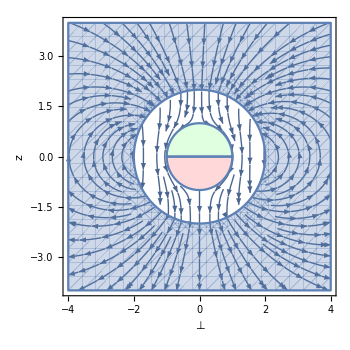

magnetic_r2=inf.png

```mathematica
(*r2->∞*)
SetDirectory[NotebookDirectory[]]
ϕ[r_,θ_,n_]:=Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*1/(3(1+l)-2^(2l+1)(5l+4))*
(Boole[1≤r≤2](3(1+l)*r^l+-2^(2l+1)(5l+4)*r^(-l-1))+
Boole[2≤r](-(1+2l)2^(2l+1)*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*1/(3(1+2l)-2^(4l+1)(10l+4))*
(Boole[1≤r≤2](3(1+2l)*r^(2l)+-2^(4l+1)(10l+4)*r^(-2l-1))+
Boole[2≤r](-(1+4l)2^(4l+1)*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas y derivapara graficar los campos*)

χ[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ϕ[r,θ,4],{r,θ}->{x,y}]];
{Ex,Ey}={Simplify[-D[χ[x,y],x]],Simplify[-D[χ[x,y],y]]};
(*electricr2=Show[StreamPlot[ {Ex,Ey},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{4≤x^2+y^2},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["electric_r2=inf.png",electricr2,ImageResolution->600]*)


ψ[r_,θ_,n_]:=
Simplify[
Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*1/(3(1+l)-2^(2l+1)(5l+4))*
(Boole[1≤r≤2](-(1+l)*r^l-l*r^(-l-1))+
Boole[2≤r](-l(1-2^(2l+1))*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*1/(3(1+2l)-2^(4l+1)(10l+4))*
(Boole[1≤r≤2](-(1+2l)*r^(2l)-2l*r^(-2l-1))+
Boole[2≤r](-2l(1-2^(4l+1))*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas para graficar los campos*)

ω[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ψ[r,θ,3],{r,θ}->{x,y}]];
{Bx,By}={Simplify[-D[ω[x,y],x]],Simplify[-D[ω[x,y],y]]};
magneticr2=Show[StreamPlot[ {Bx,By},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{4≤x^2+y^2},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["magnetic_r2=inf.png",magneticr2,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\Physics\TESIS\Avances

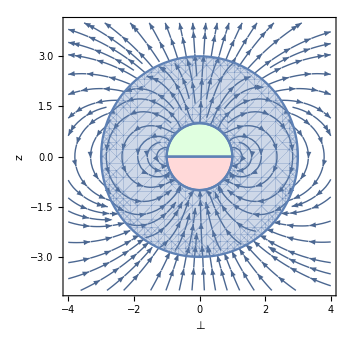

electric_r1=a.png

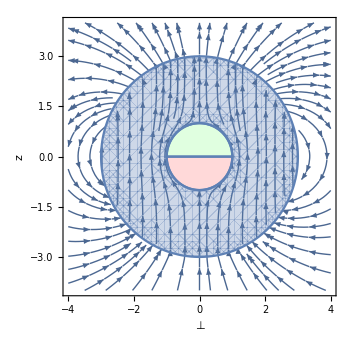

magnetic_r1=a.png

```mathematica
(*r1=a*)
SetDirectory[NotebookDirectory[]]
ϕ[r_,θ_,n_]:=
Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,1,3,4,1,l]*
(Boole[1≤r≤3](a2[1,1,3,4,1,l]*r^l+b2[1,1,3,4,1,l]*r^(-l-1))+
Boole[3≤r](b3[1,1,3,4,1,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,1,3,4,1,2l]*
(Boole[1≤r≤3](a2[1,1,3,4,1,2l]*r^(2l)+b2[1,1,3,4,1,2l]*r^(-2l-1))+
Boole[3≤r](b3[1,1,3,4,1,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas y derivapara graficar los campos*)

χ[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ϕ[r,θ,4],{r,θ}->{x,y}]];
{Ex,Ey}={Simplify[-D[χ[x,y],x]],Simplify[-D[χ[x,y],y]]};
electricr1=Show[StreamPlot[ {Ex,Ey},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{1≤x^2+y^2≤9},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["electric_r1=a.png",electricr1,ImageResolution->600]

ψ[r_,θ_,n_]:=
Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,1,3,4,1,l]*
(Boole[1≤r≤3](c2[1,1,3,4,1,l]*r^l+d2[1,1,3,4,1,l]*r^(-l-1))+
Boole[3≤r](d3[1,1,3,4,1,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,1,3,4,1,2l]*
(Boole[1≤r≤3](c2[1,1,3,4,1,2l]*r^(2l)+d2[1,1,3,4,1,2l]*r^(-2l-1))+
Boole[3≤r](d3[1,1,3,4,1,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas para graficar los campos*)

ω[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ψ[r,θ,4],{r,θ}->{x,y}]];
{Bx,By}={Simplify[-D[ω[x,y],x]],Simplify[-D[ω[x,y],y]]};
magneticr1=Show[StreamPlot[ {Bx,By},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],
RegionPlot[{1≤x^2+y^2≤9},{x,-4,4},{y,-4,4},PlotRange->All],AxesStyle->Black,ImageSize->350
]
Export["magnetic_r1=a.png",magneticr1,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\Physics\TESIS\Avances

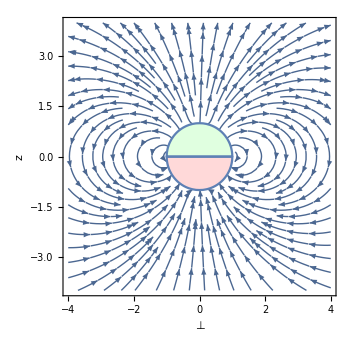

electric_jackson.png

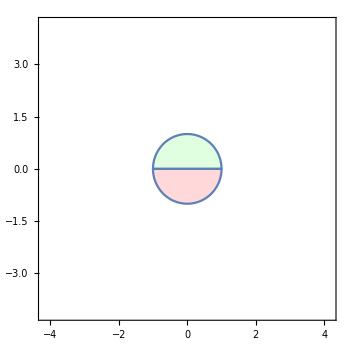

```mathematica
(*JACKSON*)
SetDirectory[NotebookDirectory[]]
ϕ[r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,2,3,1,0,l]*
(Boole[1≤r≤2](a1[1,2,3,1,0,l]*r^l+b1[1,2,3,1,0,l]*r^(-l-1))+
Boole[2≤r≤3](a2[1,2,3,1,0,l]*r^l+b2[1,2,3,1,0,l]*r^(-l-1))+
Boole[3≤r](b3[1,2,3,1,0,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,2,3,1,0,2l]*
(Boole[1≤r≤2](a1[1,2,3,1,0,2l]*r^(2l)+b1[1,2,3,1,0,2l]*r^(-2l-1))+
Boole[2≤r≤3](a2[1,2,3,1,0,2l]*r^(2l)+b2[1,2,3,1,0,2l]*r^(-2l-1))+
Boole[3≤r](b3[1,2,3,1,0,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas y derivapara graficar los campos*)

χ[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ϕ[r,θ,4],{r,θ}->{x,y}]];
{Ex,Ey}={Simplify[-D[χ[x,y],x]],Simplify[-D[χ[x,y],y]]};
electricjackson=Show[StreamPlot[ {Ex,Ey},{x,-4,4},{y,-4,4},PlotRange->All,FrameLabel->{Style["⊥",12],Style[z,12]}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotRange->All,PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotRange->All,PlotStyle->LightRed],AxesStyle->Black,ImageSize->350
]
Export["electric_jackson.png",electricjackson,ImageResolution->600]

ψ[r_,θ_,n_]:=
Simplify[
Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[1,2,3,1,0,l]*
(Boole[1≤r≤2](c1[1,2,3,1,0,l]*r^l+d1[1,2,3,1,0,l]*r^(-l-1))+
Boole[2≤r≤3](c2[1,2,3,1,0,l]*r^l+d2[1,2,3,1,0,l]*r^(-l-1))+
Boole[3≤r](d3[1,2,3,1,0,l]*r^(-l-1)))
*LegendreP[l,Sin[θ]],{l,1,2*n+1}]-
Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[1,2,3,1,0,2l]*
(Boole[1≤r≤2](c1[1,2,3,1,0,2l]*r^(2l)+d1[1,2,3,1,0,2l]*r^(-2l-1))+
Boole[2≤r≤3](c2[1,2,3,1,0,2l]*r^(2l)+d2[1,2,3,1,0,2l]*r^(-2l-1))+
Boole[3≤r](d3[1,2,3,1,0,2l]*r^(-2l-1)))
*LegendreP[2l,Sin[θ]],{l,1,n}]];
(*r va de 1 a 2 y theta de 0 a Pi. n da lugar a un número impar 2n+1 que especifica la potencia de la serie. Cambiamos a cartesianas para graficar los campos*)

ω[x_,y_]:=Simplify[TransformedField["Polar"->"Cartesian",ψ[r,θ,4],{r,θ}->{x,y}]];
{Bx,By}={Simplify[-D[ω[x,y],x]],Simplify[-D[ω[x,y],y]]};
Show[StreamPlot[ {Bx,By},{x,-4,4},{y,-4,4}],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,4},PlotStyle->LightGreen],
RegionPlot[x^2+y^2≤1,{x,-4,4},{y,0,-4},PlotStyle->LightRed],AxesStyle->Black,ImageSize->350
]
```